# AdaptiveEvolution

Run an adaptive search within any generative computational system

## Definition

```mathematica
SymIndexMap[k_,r_]:=SymIndexMap[k,r]=With[
{tups=Tuples[Reverse[Range[0,k-1]],2r+1]},
Sort[Catenate[MapIndexed[{Position[tups,#][[1,1]],#2[[1]]}&,
GatherBy[tups,Sort[{#,Reverse[#]}]&],{2}]]]
]
```

```mathematica
SymUp[k_,r_]:=SymUp[k,r
]=SymIndexMap[k,r][[All,2]]
```

```mathematica
SymDown[k_,r_]:=SymDown[k,r
]=Values[KeySort[Map[First,
GroupBy[SymIndexMap[k,r],
Last->First]]]]
```

```mathematica
RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]
```

```mathematica
TestLifetime[rule_,init_List:{1},
max_Integer:100(*,infinity_:Infinity*)]:=With[
{array=CellularAutomaton[rule,{init,0},{max,All}]},If[#==0,-Infinity(*-infinity*),max-#+1]&[
LengthWhile[Reverse[array],Total[#]==0&]
]
]
```

```mathematica
ClearAll[AdaptiveEvolution];Options[AdaptiveEvolution] = {"MutationFunction"->RandomRuleMutation, "FitnessFunction"->(TestLifetime[#]&),"SelectionFunction"->(#1>= #2&), "InitialFitness"->Automatic, "HaltCondition"->None, "SearchHistory"->True};
AdaptiveEvolution[rule_, steps_, OptionsPattern[AdaptiveEvolution]]:=Module[{},
If[OptionValue["SearchHistory"], NestList, Nest][
(Block[{newrule= OptionValue["MutationFunction"][#rule], newfitness},
newfitness = OptionValue["FitnessFunction"][newrule];
AssociationThread[{"rule", "fitness"}-> If[OptionValue["SelectionFunction"][newfitness, #fitness], {newrule, newfitness}, {#rule, #fitness}]]]
&),
<|"rule"-> rule, "fitness"-> If[OptionValue["InitialFitness"] === Automatic, OptionValue["FitnessFunction"][rule], OptionValue["InitialFitness"]]|>,
steps
]
]
```

## Documentation

### Usage

MyFunction[arg]

explanation of what use of the argument arg does.

### Details & Options

Additional information about usage and options.

## Examples

### Basic Examples

Starting from the null rule, adaptively search three steps for cellular automata with progressively longer halting length:

```mathematica
AdaptiveEvolution[{0, 2, 1}, 3]
```

{<|rule→{0,2,1},fitness→1|>,<|rule→{32,2,1},fitness→1|>,<|rule→{40,2,1},fitness→1|>,<|rule→{32,2,1},fitness→1|>}

### Scope

Run an adaptive search for 1000 steps for k = 3, r = 1 cellular automata with progressively longer halting lengths:

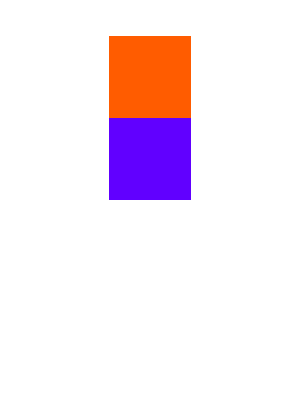
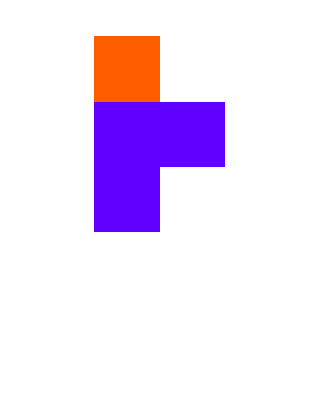
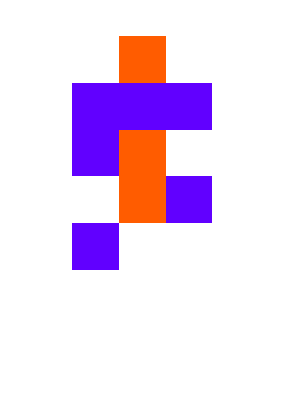
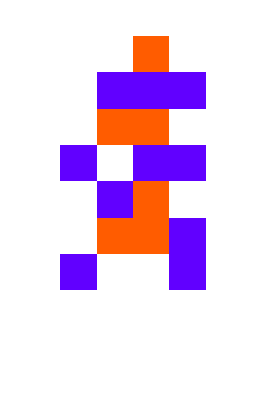
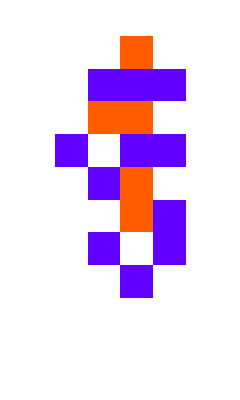
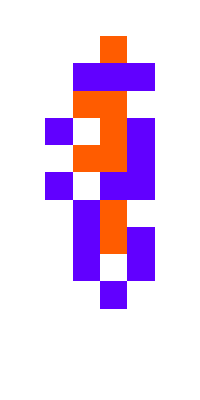
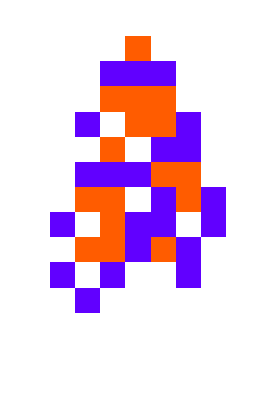
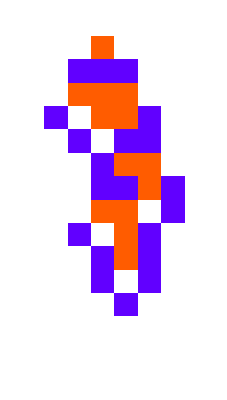
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[222344 + 2];ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#rule, {{1}, 0}, #fitness+1], ImageSize->12Sqrt[#fitness]]&/@ GatherBy[AdaptiveEvolution[{0, 3, 1}, 1000], Last][[All, 1]]
```

```mathematica
GatherBy[AdaptiveEvolution[{0, 3, 1}, 1000], Last][[All, 1]]
```

{<|rule→{0,3,1},fitness→1|>,<|rule→{354518464932,3,1},fitness→-∞|>}

Adaptively evolve cellular automata that are less compressible:

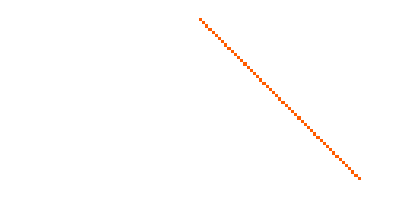
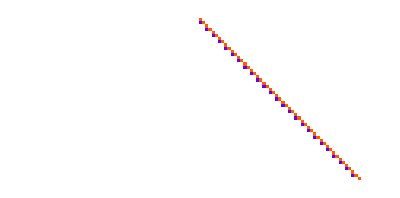
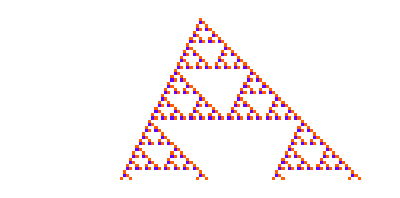
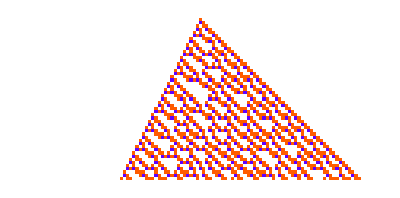
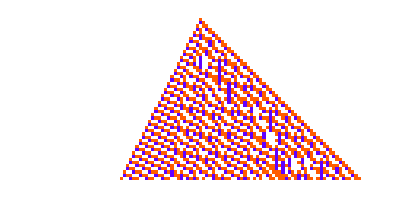
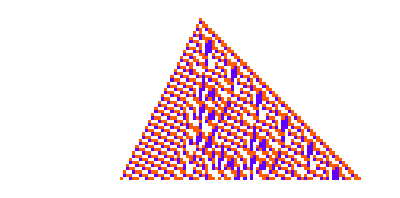
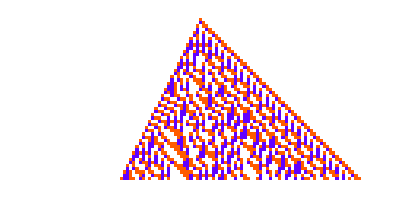
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[222344 + 2];ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#rule, {{1}, 0}, {50,All}], ImageSize->Automatic]&/@ GatherBy[
AdaptiveEvolution[{0, 3, 1}, 30, "FitnessFunction"-> (StringLength[Compress[CellularAutomaton[#, {{1}, 0}, 100]]]&)],
 Last][[All, 1]]
```

Adaptively search for cellular automata that are more compressible:

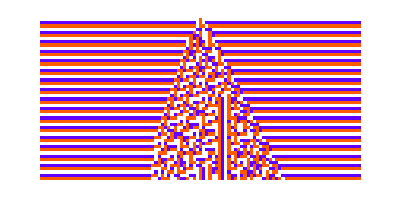
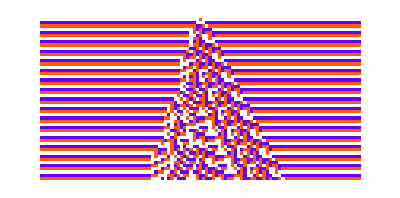
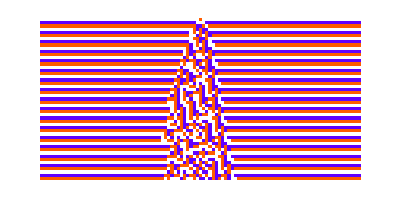
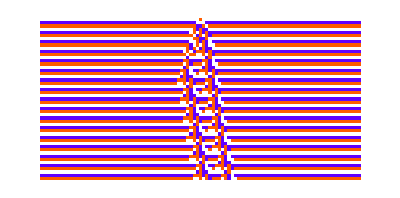
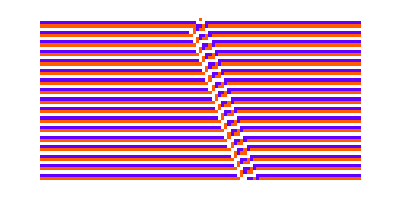
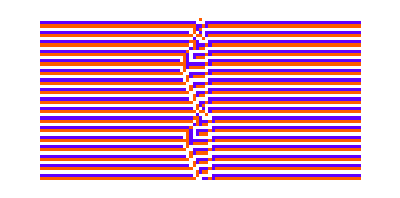
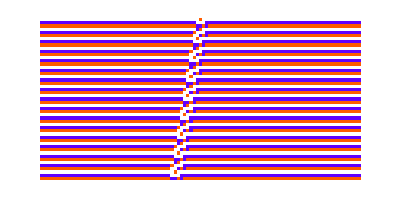

```mathematica
SeedRandom[222344 + 8];ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#rule, {{1}, 0}, {50,All}], ImageSize->Automatic]&/@ GatherBy[AdaptiveEvolution[{ResourceFunction["RandomCA"][{3, 1}]["RuleNumber"], 3, 1}, 30, "FitnessFunction"-> (-StringLength[Compress[CellularAutomaton[#, {{1}, 0}, 100]]]&)], Last][[All, 1]]
```

Search for CAs whose density approximates a sine wave

```mathematica
SeedRandom[444110 + 6];
exampleevolution = 
AdaptiveEvolution[{0, 4, 1}, 2000,
"MutationFunction"->( RandomRuleMutation[#, 1, "Symmetric"->True]&),
 "FitnessFunction"-> (-Total[Abs[(Count[#, x_/;x>0] / 200&/@ CellularAutomaton[#, {{1}, 0}, {100, {-100, 100}}]) - sf]]&)];
```

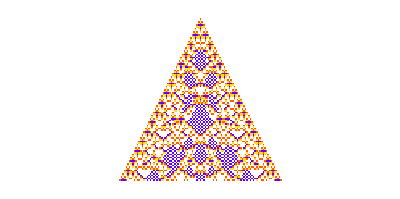
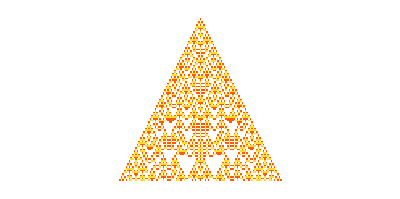
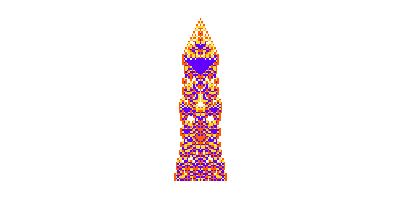
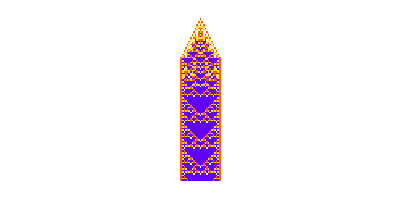
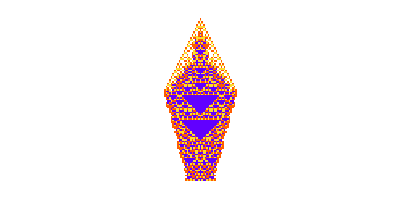
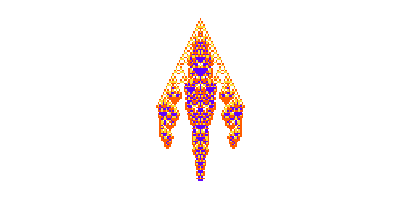
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#rule, {{1}, 0}, {100, {-100, 100}}], ImageSize->Automatic]&/@ GatherBy[#, Last][[1;;All;;3, 1]]&@ exampleevolution
```

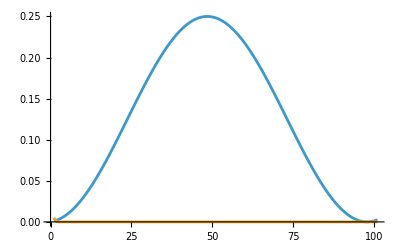
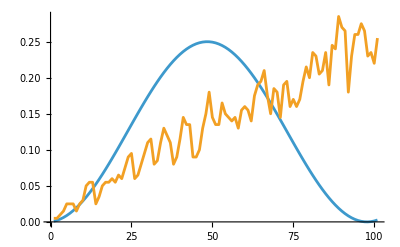
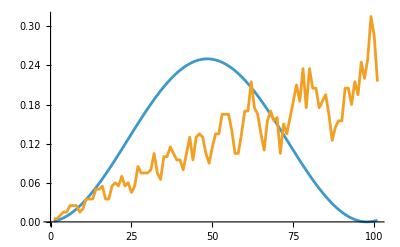
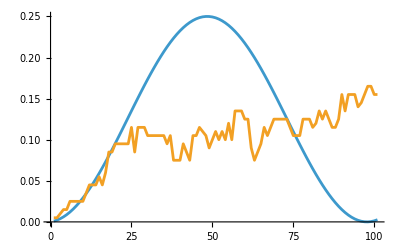
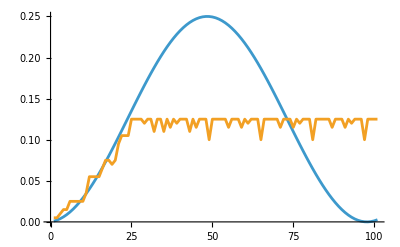
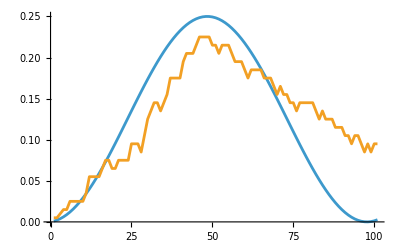
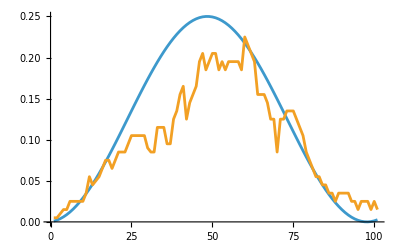

```mathematica
ListLinePlot[{sf, #}]&/@(Count[#, x_/;x>0] / 200&/@ CellularAutomaton[#rule, {{1}, 0}, {100, {-100, 100}}]&)/@ GatherBy[#, Last][[1;;All;;3, 1]]&@ exampleevolution
```

```mathematica
ResourceFunction["WolframModel"][{{{x,y}}->{{z,y},{y,x}}},{{1,2}},8]["StatesPlotsList","MaxImageSize"->180]
```

```mathematica
ResourceFunction["WolframModelPlot"][#,"MaxImageSize"->100]&/@ResourceFunction["WolframModel"][{{x,y}}->{{y,z},{z,x}},{{1,1}},5,"StatesList"]
```

### Options

### Applications

### Properties and Relations

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Author Name

### Keywords

keyword 1

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

SymbolName (documented Wolfram Language symbol)

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.